```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"mathematica","packages"}]];
Get["SciDraw`"];
```

SetDelayed::write: Tag BoundingRegion in BoundingRegion[ObjectList:{(_Object?(And[«2»]&)|_?(And[«2»]&)|_Object?(And[«2»]&)|_?(And[«2»]&))..}] is Protected.

SetDelayed::write: Tag BoundingRegion in BoundingRegion[obj:_Object?(ObjectExistsQ[Slot[«1»]]&&MemberQ[ClassAncestry[«1»],FigAnchor]&)|_?(ObjectExistsQ[Object[«1»]]&&MemberQ[ClassAncestry[«1»],FigAnchor]&)|_Object?(ObjectExistsQ[Slot[«1»]]&&MemberQ[ClassAncestry[«1»],FigObject]&)|_?(ObjectExistsQ[Object[«1»]]&&MemberQ[ClassAncestry[«1»],FigObject]&)] is Protected.

SetDelayed::write: Tag MissingQ in MissingQ[expr_] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.7 (March 28, 2015)
View color paletteVisit home page  -Graphics-

Level scheme for Te-132 based on the datafiles gamma.spe (singles) and gg.esc (doubles). Any spin-parity assignments are taken from the ENSDF, because they were not able to assigned from the data alone.
All energies of gamma-ray transitions are taken from fits made in gf3 in the file gamma.spe.
No uncertainties have been included for this trial run of building a level scheme.

```mathematica
wh=5;(*WingHeight parameter for when two levels are too close together*)
Figure[
FigurePanel[
{
(*level format options*)
SetOptions[FigObject,FontSize->12];
SetOptions[Lev,LineThickness->2,RightLabel->Automatic,RightTextOffset->BottomRight,LeftTextOffset->BottomLeft,WingTipWidth->30,Margin->0];

(* levels *)
Lev⟦"lev0"⟧[0,1,"0",LeftLabel->LabelJP[0,+1]];
Lev⟦"lev973"⟧[0,1,"973.1",LeftLabel->LabelJP[2,+1]];
Lev⟦"lev1669"⟧[0,1,"1669.4",LeftLabel->LabelJP[4,+1],WingHeight->-wh];Lev⟦"lev2105"⟧[0,1,"2105.6"];
Lev⟦"lev2485"⟧[0,1,"2485.2",WingHeight->+5wh];
Lev⟦"lev1774"⟧[0,1,"1773.9",LeftLabel->LabelJP[6,+1],WingHeight->+wh];
Lev⟦"lev2409"⟧[0,1,"2409.3",WingHeight->-wh];
Lev⟦"lev3560"⟧[0,1,"3560.3"];
Lev⟦"lev2763"⟧[0,1,"2762.8",WingHeight->+3wh];
Lev⟦"lev2484"⟧[0,1,"2484.6",WingHeight->wh];
SetOptions[Lev,LineDashing->4];
Lev⟦"lev2277"⟧[0,1,"2277.6"];
SetOptions[Lev,LineDashing->None];

(* autospaced transitions *)
SetOptions[Trans,TextBackground->Automatic,TextMargin->1,TextNudge->2];
AutoLevelInit[0.85,-0.04,-0.08];
AutoLevel["lev973"];
AutoTrans["lev0",TailLabel->"973.1"];
AutoLevel["lev2484"];
AutoTrans["lev973",TailLabel->"1511.5"];
AutoLevel["lev1669"];
AutoTrans["lev973",TailLabel->"696.3"];
AutoLevel["lev2105"];
AutoTrans["lev973",TailLabel->"1132.5"];
AutoLevel["lev1774"];
AutoTrans["lev1669",TailLabel->"104.5"];
AutoLevel["lev2485"];
AutoTrans["lev1669",TailLabel->"815.8"];
AutoLevel["lev2409"];
AutoTrans["lev1774",TailLabel->"635.44"];
AutoLevel["lev2763"];
AutoTrans["lev1774",TailLabel->"988.9"];
AutoLevel["lev3560"];
AutoTrans["lev2409",TailLabel->"1151.0"];
AutoLevel["lev2277"];
AutoTrans["lev0",TailLabel->"2277.6"];
FigLabel[Scaled[{0.5,0.97}],Isotope[132,"Te"],FontSize->16]
},
PlotRange->{{-0.1,1.1},{-20,4200}},Frame->False
],
CanvasSize->{6,8}
]
```

-Graphics-

```mathematica
973.1+1511.5
```

2484.6

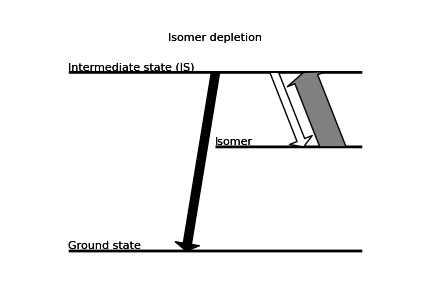

```mathematica
wh=5;(*WingHeight parameter for when two levels are too close together*)
Figure[
FigurePanel[
{
(*level format options*)
SetOptions[FigObject,FontSize->24];
SetOptions[Lev,LineThickness->2,RightLabel->None,RightTextOffset->BottomRight,LeftTextOffset->BottomLeft,WingTipWidth->30,Margin->0];
SetOptions[Trans,CenterTextOrientation->Horizontal,CenterTextBackground->Automatic
];
DefineStyle["up",{Trans->{FillColor->Gray,ArrowType->Block,HeadLength->9,HeadLip->10,Width->30,CenterTextColor->Firebrick}}];
DefineStyle["down",{Trans->{FillColor->Black,ArrowType->Block,HeadLength->9,HeadLip->10,Width->10}}];
DefineStyle["back",{Trans->{FillColor->White,ArrowType->Block,HeadLength->9,HeadLip->10,Width->10}}];

(* levels *)
Lev⟦"lev0"⟧[0,1,"0",LeftLabel->"Ground state",FontSize->20];
Lev⟦"lev973"⟧[0.5,1,"973.1",LeftLabel->"Isomer",FontSize->20];
Lev⟦"lev1669"⟧[0,1,"1669.4",LeftLabel->"Intermediate state (IS)",FontSize->20];

(* autospaced transitions *)
AutoLevelInit[0.85,-0.04,-0.08];
AutoLevel["lev973"];
Trans["lev973",0.4,"lev1669",0.8,Style->"up"];
Trans["lev1669",0.5,"lev0",0.4,Style->"down"];
Trans["lev1669",0.7,"lev973",0.3,Style->"back"];
(*AutoTrans["lev0"];*)
AutoLevel["lev1669"];
(*AutoTrans["lev973"];*)
FigLabel[Scaled[{0.5,0.95}],"Isomer depletion",FontSize->24]
},
PlotRange->{{-0.1,1.1},{-100,2100}},Frame->False
],
CanvasSize->{6,4},CanvasMargin->0.2
]
```